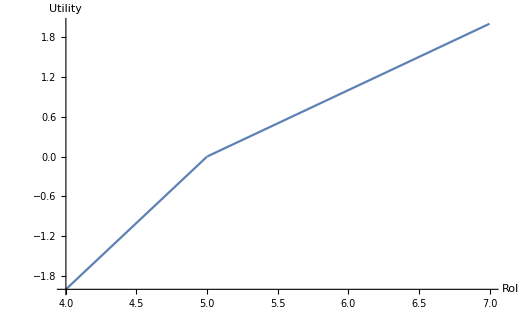

```mathematica
Plot[Max[x-5,0]-2Max[5-x,0],{x,4,7},AxesLabel->{"RoI","Utility"},AxesOrigin->{4,-2},BaseStyle->{FontFamily->"Latin Modern Roman",FontSize->14}]
```

```mathematica
stocks={"MSFT","AAPL","GOOG"};
y=2015;
```

```mathematica
ans=solveObjective[{"MSFT","AAPL","GOOG"},2015]
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
q=ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

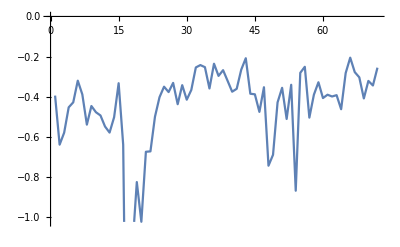

```mathematica
ListLinePlot[xs.ans]
```

```mathematica
rangeVars[q,7]
```

{q$1,q$2,q$3,q$4,q$5,q$6,q$7}

```mathematica
ans=%
```

{q$1→-0.462577,q$2→0.0813624,q$3→0.118456,q$4→0.0476892,q$5→0.0255442,q$6→0.145512,q$7→-0.860971}

```mathematica
rangeVars[q,7]/.ans
```

{-0.462577,0.0813624,0.118456,0.0476892,0.0255442,0.145512,-0.860971}

```mathematica
xs=adjustFeaturesMatrix[x[y]/@stocks];
rs=Flatten[r[y]/@stocks,1];
```

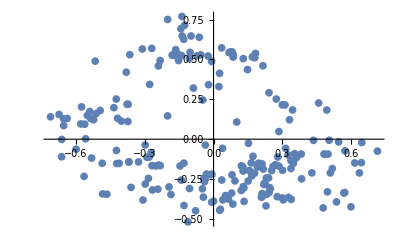

```mathematica
ListPlot@
Flatten[
Map[Function[xStock,
(*#[[3;;4]]&/@xStock]*)
Transpose@MapThread[Standardize[{##},Mean,Function[3StandardDeviation[##]]]&,#[[3;;4]]&/@xStock]],
xs],
1]
```

```mathematica
{a,b,c}≥{1,2,3}
```

{4,b,c}≥{1,2,3}

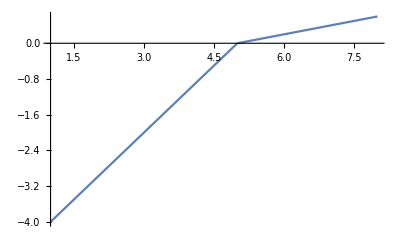

```mathematica
U[p_]:=0.2 (p-5)+Min[(1-0.2)*(p-5),0];
Plot[U[p],{p,1,8}]
```

```mathematica
stocks={"AAPL","GOOGL","MSFT","F"};
y=2014;
```

```mathematica
solveObjective[stocks,y]
```

>>  
Calling SDPT3 4.0: 2607 variables, 1300 equality constraints
------------------------------------------------------------

 num. of constraints = 1300
 dim. of linear var  = 2600
 dim. of free   var  =  7 *** convert ublk to lblk
 number of dense column in A = 14
*******************************************************************
   SDPT3: Infeasible path-following algorithms
*******************************************************************
 version  predcorr  gam  expon  scale_data
    NT      1      0.000   1        0    
it pstep dstep pinfeas dinfeas  gap      prim-obj      dual-obj    cputime
-------------------------------------------------------------------
 0|0.000|0.000|9.4e-03|6.9e+01|6.8e+06| 6.628725e+04  0.000000e+00| 0:0:00| spchol  1  1 
 1|1.000|0.950|1.3e-05|3.7e+00|4.2e+05| 6.445150e+04  1.614177e-01| 0:0:00| spchol  1  1 
 2|1.000|0.128|3.7e-05|3.3e+00|5.1e+05| 8.673619e+04  1.615428e-01| 0:0:00| spchol  1  1 
 3|1.000|0.772|2.7e-06|7.7e-01|1.6e+05| 7.407803e+04  1.675399e-01| 0:0:00| spchol  1  1 
 4|1.000|0.519|1.4e-06|3.7e-01|6.5e+04| 4.145518e+04  1.681265e-01| 0:0:00| spchol  1  1 
 5|1.000|0.511|1.8e-08|1.8e-01|2.1e+04| 1.608650e+04  1.684221e-01| 0:0:00| spchol  1  1 
 6|1.000|0.535|1.3e-09|8.6e-02|4.4e+03| 3.874323e+03  1.685797e-01| 0:0:00| spchol  1  1 
 7|1.000|0.651|4.8e-11|3.0e-02|4.9e+02| 4.661837e+02  1.686905e-01| 0:0:00| spchol  1  1 
 8|0.990|0.812|3.0e-12|5.7e-03|3.1e+01| 3.056391e+01  1.688456e-01| 0:0:00| spchol  1  1 
 9|0.978|0.981|5.8e-12|1.1e-04|6.7e-01| 8.404123e-01  1.706344e-01| 0:0:00| spchol  1  1 
10|0.870|0.844|2.4e-09|1.7e-05|1.2e-01| 3.606867e-01  2.366410e-01| 0:0:00| spchol  2  2 
11|0.882|0.140|3.1e-10|1.5e-05|1.1e-01| 3.579841e-01  2.487068e-01| 0:0:00| spchol  2  2 
12|1.000|0.806|2.3e-11|3.5e-06|4.3e-02| 3.514207e-01  3.084373e-01| 0:0:00| spchol  1  2 
13|1.000|0.678|2.8e-12|1.2e-06|1.9e-02| 3.374631e-01  3.188637e-01| 0:0:00| spchol  2  2 
14|0.940|0.952|6.3e-13|3.6e-07|7.8e-03| 3.337214e-01  3.258864e-01| 0:0:00| spchol  2  2 
15|1.000|0.952|3.1e-12|1.5e-07|2.0e-03| 3.305599e-01  3.285875e-01| 0:0:00| spchol  1  1 
16|1.000|0.957|3.8e-11|3.8e-08|5.3e-04| 3.298614e-01  3.293277e-01| 0:0:00| spchol  1  1 
17|0.794|0.953|6.6e-11|1.0e-08|1.8e-04| 3.297116e-01  3.295323e-01| 0:0:00| spchol  1  2 
18|1.000|0.958|5.7e-12|3.5e-09|4.6e-05| 3.296294e-01  3.295832e-01| 0:0:00| spchol  2  2 
19|1.000|0.985|3.6e-12|8.9e-10|2.7e-06| 3.296085e-01  3.296058e-01| 0:0:00| spchol  2  2 
20|1.000|0.989|1.6e-11|5.2e-11|5.7e-08| 3.296073e-01  3.296073e-01| 0:0:00| spchol 10 14 
21|1.000|0.989|2.1e-09|1.9e-12|1.0e-09| 3.296073e-01  3.296073e-01| 0:0:00|
  stop: max(relative gap, infeasibilities) < 1.49e-08
-------------------------------------------------------------------
 number of iterations   = 21
 primal objective value =  3.29607292e-01
 dual   objective value =  3.29607291e-01
 gap := trace(XZ)       = 1.03e-09
 relative gap           = 6.22e-10
 actual relative gap    = 2.98e-10
 rel. primal infeas (scaled problem)   = 2.12e-09
 rel. dual     "        "       "      = 1.93e-12
 rel. primal infeas (unscaled problem) = 0.00e+00
 rel. dual     "        "       "      = 0.00e+00
 norm(X), norm(y), norm(Z) = 1.3e-02, 3.5e+01, 3.6e+01
 norm(A), norm(b), norm(C) = 5.2e+01, 1.0e+00, 3.7e+01
 Total CPU time (secs)  = 0.30  
 CPU time per iteration = 0.01  
 termination code       =  0
 DIMACS: 2.1e-09  0.0e+00  3.6e-11  0.0e+00  3.0e-10  6.2e-10
-------------------------------------------------------------------
 
------------------------------------------------------------
Status: Solved
Optimal value (cvx_optval): -0.415058

{0.00700528,0.000106705,-0.0000344275,-0.0021256,0.00210407,0.0000398939,0.000033368}

```mathematica
Times[a,b,c]
```

a b c

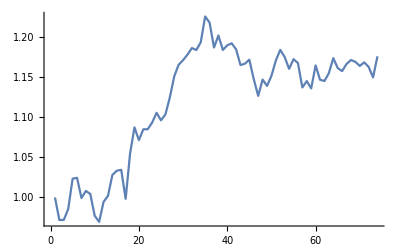

```mathematica
ListLinePlot[Last@rawReturns[{"AAPL"},2015]]
```

```mathematica
ans=%
```

{0.971828,0.97192,0.985548,1.02342,1.02451,0.999268,1.00814,1.0043,0.977042,0.96945,0.99442,1.00201,1.02808,1.03339,1.03448,0.998262,1.0547,1.08753,1.07162,1.08506,1.08525,1.09357,1.10569,1.09638,1.10366,1.12487,1.15123,1.1658,1.17151,1.17843,1.18663,1.18414,1.19382,1.22609,1.21844,1.18728,1.2023,1.18423,1.19004,1.19253,1.18497,1.16534,1.16709,1.17207,1.14782,1.12689,1.14727,1.13934,1.15188,1.17114,1.18433,1.17538,1.16063,1.17271,1.16792,1.1374,1.14533,1.1362,1.16497,1.14708,1.14542,1.15529,1.174,1.16165,1.15787,1.16672,1.1717,1.16939,1.16432,1.16875,1.16312,1.15003,1.17631}

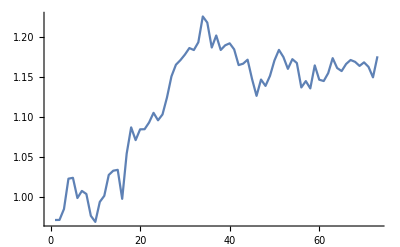

```mathematica
ListLinePlot[ans]
```